## Rouse Eigenbasis

```mathematica
v[p_,n_,N_]:=If[p==0,√1/N,√2/N Cos[(n-1/2)(p*π)/N]]
V[N_]:=Table[v[p,n,N],{p,0,N-1},{n,N}]
```

## Average DSB Laplacian Matrix

Only the first monomer of the two-DSB cluster is random, uniformly distributed over all the allowed region ℓ which is defined naturally by N and g.

```mathematica
ℓ[N_,g_]:=N-g-4
𝒸[m_,N_,g_]:=Piecewise[{{4,Abs[m-(N+1)/2]≤(N-1)/2-g-3},{3,Abs[m-(N+1)/2]==(N-1)/2-g-2},{2,Abs[m-(N+1)/2]≤ (N-1)/2-2},{1,Abs[m-(N+1)/2]==(N-1)/2-1},{0,Abs[m-(N+1)/2]==(N-1)/2}}]
```

The probability of being broken is, for each monomer:

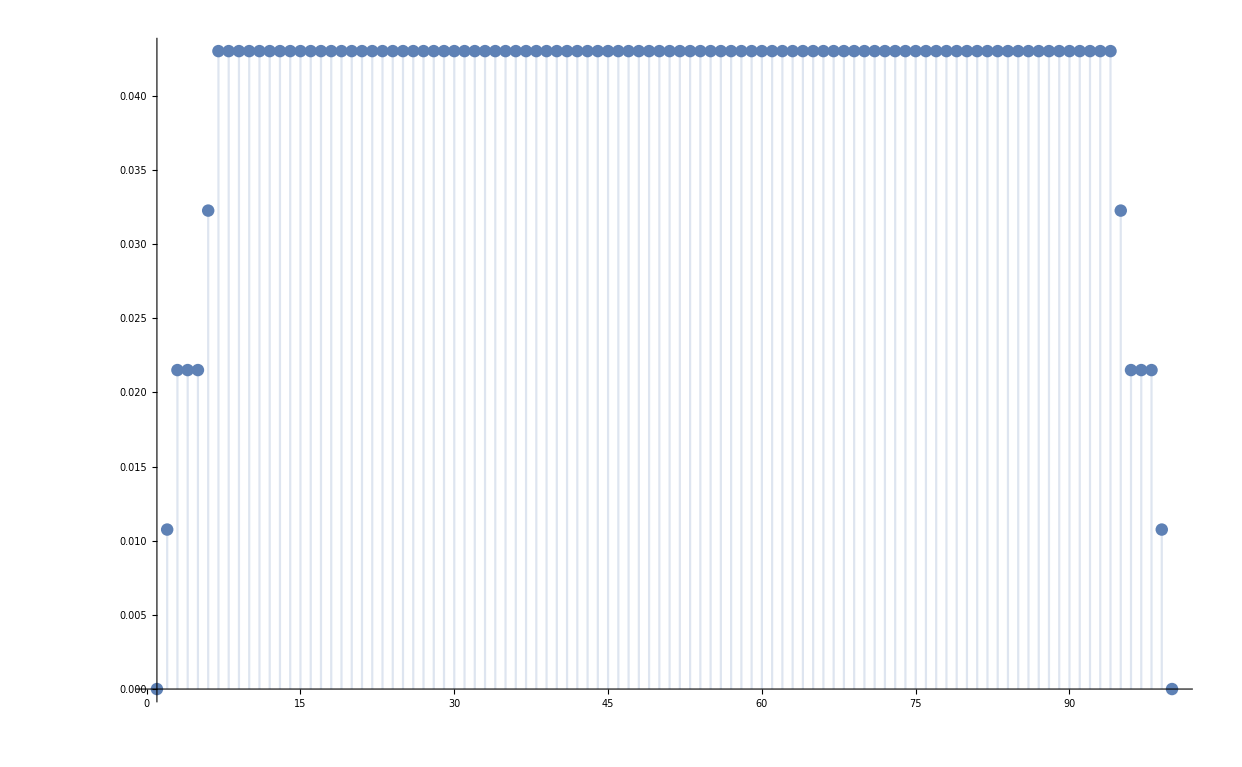

```mathematica
DiscretePlot[𝒸[m,100,3]/ℓ[100,3],{m,1,100}]
```

In effect, the expected number of broken monomers corresponds with the actual number of broken monomers (4):

```mathematica
∑_(m=1)^100 𝒸[m,100,3]/ℓ[100,3]
```

4

Finally, the average DSB Laplacian Matrix ⟨X⟩ is:

```mathematica
Xoff[N_,g_]:= SparseArray[{{i_,j_}:>-𝒸[i,N,g]/;((Abs[i-j]==1) && (N >j >1))},{N,N}]
X[N_,g_]:=1/(N-g-3)*(Xoff[N,g]-DiagonalMatrix[Total[Xoff[N,g],{2}]])
```

```mathematica
MatrixForm[X[30,4]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/23 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/23 | 8/23 | -4/23 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/23 | 6/23 | -3/23 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/23 | 4/23 | -2/23 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/23 | 1/23 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Eigenvalues of the average DSB Laplacian matrix

We compute the pseudo-diagonal matrix using the Rouse eigenbasis

```mathematica
pseudoDiagX[N_,g_]:=V[N].X[N,g].Transpose[V[N]]
```

```mathematica
ListPlot3D[pseudoDiagX[50,10],PlotRange->Full]
```

-Graphics3D-

We compare the diagonal of V.,⟨X⟩.V^T with the real (numerically computed) eigenvalues of ⟨X⟩.

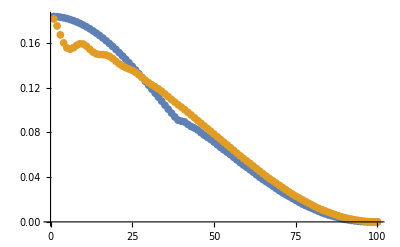

```mathematica
ListPlot[{Eigenvalues[X[100,10]],Reverse[Diagonal[pseudoDiagX[100,10]]]}]
```

⟨X⟩(g) can also be written as D_g M where M is the Rouse matrix and

```mathematica
Dg[N_,g_]:=SparseArray[{{i_,j_}:>𝒸[i,N,g]/;i==j},{N,N}]
```

For instance:

```mathematica
Dg[15,3] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Since V.,⟨X⟩.V^T = V.,D_g.M.V^T=V.,D_g.V^T.V.M.V^T=V.,D_g.V^T.Λ. and V.,D_g.V^T has a dominant diagonal,
 the diagonal elements of V.,⟨X⟩.V^T are almost equal to ω_p λ_p where ω_p are the diagonal elements of V.,D_g.V^T (perturbation) and λ_p are the Rouse eigenvalues.

```mathematica
TrigReduce[V[25].Dg[25,3].Transpose[V[25]]] // MatrixForm
```

(1)
 |  |  |  |

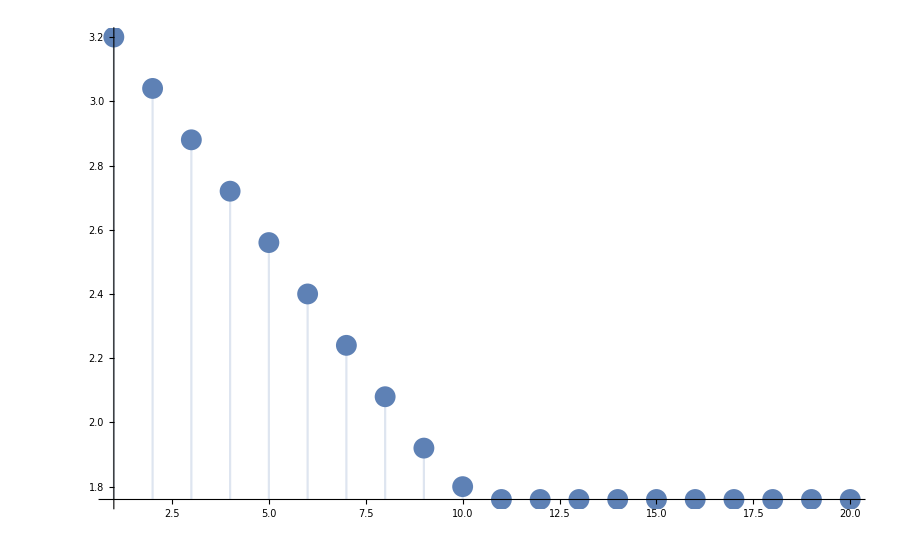

```mathematica
DiscretePlot[((V[25].Dg[25,g].Transpose[V[25]])[[1,1]]),{g,1,20}]
```

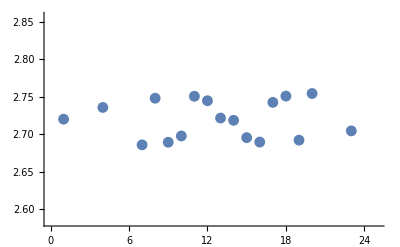

```mathematica
ListPlot[%]
```

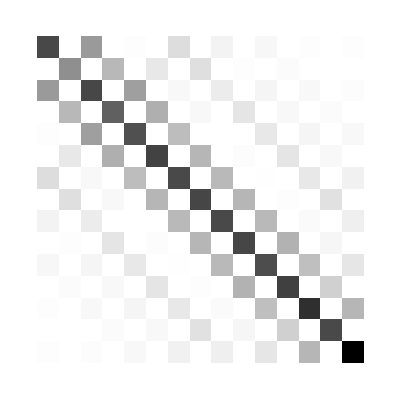

```mathematica
ArrayPlot[%]
```

```mathematica
ListPlot3D[V[100].Dg[100,10].Transpose[V[100]],PlotRange->Full]
```

-Graphics3D-

The diagonal V.,D_g.V^T seems to average the values of c

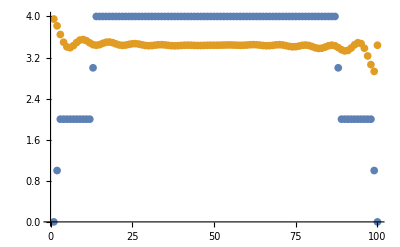

```mathematica
ListPlot[{Reverse[Diagonal[Dg[100,10]]],Reverse[Diagonal[V[100].Dg[100,10].Transpose[V[100]]]]}]
```

```mathematica
vdv[N_,g_]:=V[N].Dg[N,g].Transpose[V[N]]
Λ[N_]:=SparseArray[{{i_,j_}:>4*(Sin[((i-1)*π)/(2*N)])^2/;i==j},{N,N}]
```

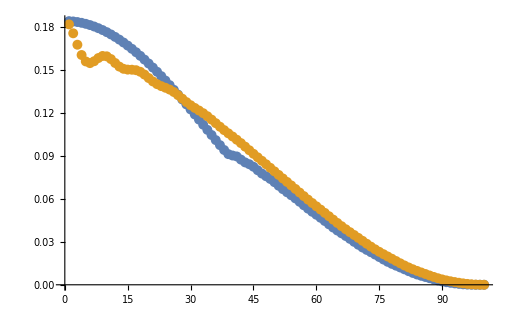

```mathematica
ListPlot[{Eigenvalues[X[100,10]],Reverse[Diagonal[1/(100-10-3)*DiagonalMatrix[Diagonal[vdv[100,10]]].Λ[100]]]}]
```